```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/25,maxt/25-maxt/75}];
```

```mathematica
pathToOutput=ToString["\..\plots\aperiodic2\\"];
```

## Step response

### TF function

```mathematica
k=10;
T3 = 0.08;
T4 = 0.04;
maxt = 0.5;
TFsimple=k/((T3*s + 1)(T4 *s +1));
TF=TransferFunctionModel[k/((T3*s + 1)(T4 *s +1)),s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Horizontal Dashed Line

```mathematica
stepLineAbove=Line[{{0,TFstableValue},{maxt,TFstableValue}}];
```

### Tangent Line

```mathematica
a=(T3*T4)/(T3-T4)*Log[T3/T4];
tangentLine =(D[TFstep,t]/.t->a)×(t-a) + (TFstep/.t->a);
```

### Vertical Dashed Line

```mathematica
sl=Solve[tangentLine==TFstep];
tangientInStable=sl[[All,1,2]][[1]];
vertLine=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
ss=Solve[tangentLine==TFstableValue];
tangientInStable=ss[[All,1,2]][[1]];
vertLine2=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

#### Vertical size

```mathematica
verSizeText=Text[
sizeText["k"],
{
-0.008,
TFstableValue
}
];
```

### Plot

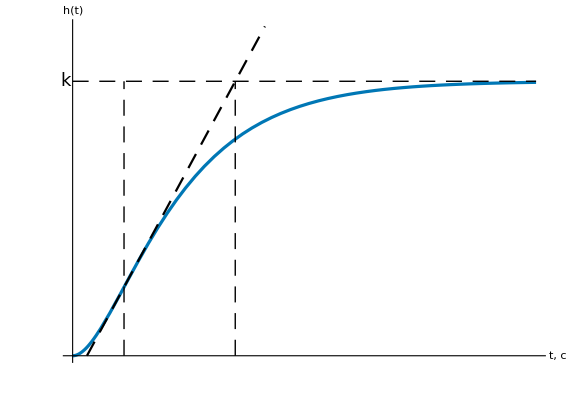

```mathematica
tickXStep = 1/10;
tickYStep = 2;
stepRespPic=Plot[{TFstep, tangentLine},{t, 0, maxt},
AxesStyle->Directive[Thickness[0.002],Black],
AxesLabel->{sizeText["t, с"], sizeText["h(t)"]},
GridLines->None,
AspectRatio->11/16,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{(#&@Array[{tickXStep #,}&,100]),(#&@Array[{tickYStep #,}&,100])},
Epilog->{
{Directive[Black,dashingStyle],stepLineAbove},
{Directive[Black,dashingStyle],vertLine},
{Directive[Black,dashingStyle],vertLine2},
{verSizeText}
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

## Bode plot

### Log Plot

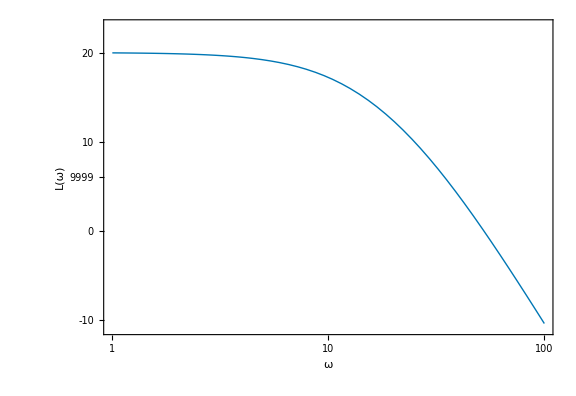

```mathematica
bodePlot=BodePlot[TF,{1,10^2},PlotRange->{{-11,23},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large
];
ampBodePlot=RestylePlot[
bodePlot[[1,1,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\aperiodic2\log-apm-freq.svg

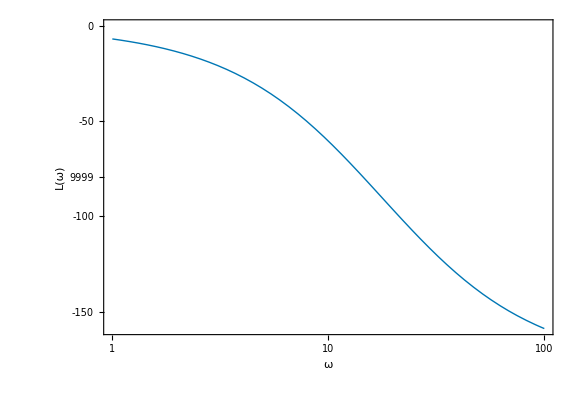

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[1,2,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\aperiodic2\log-phase-freq.svg

### Plot

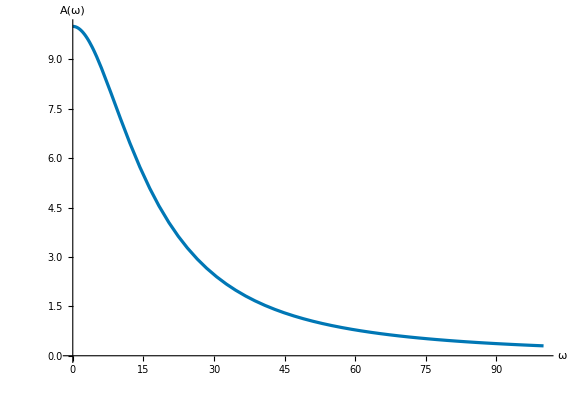

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f,0, 100},
PlotRange->{{0, 100},{0,10}},
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\aperiodic2\amp-freq.svg

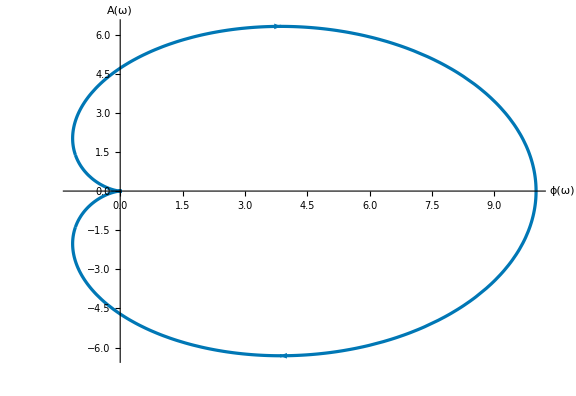

```mathematica
nyquistPlot=NyquistPlot[TF,
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ϕ(ω)"],sizeText["A(ω)"]},
AxesOrigin->{0,0},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\aperiodic2\nyquist.svg